# Yoosook' s Request

## Load Data

```mathematica
GetExperimentID[expStr_]:=ToExpression[#]&/@StringSplit[expStr,"_"][[2;;All]]
hexToRGB=RGBColor@@(IntegerDigits[ToExpression@StringReplace[#,"#"->"16^^"],256,3]/255.)&;
SetDirectory["/Volumes/marshallShare/UCI/Yoosook/tParams/islandMixed/"];
ColorBlend[a_]:=Blend[{{1,Directive[RGBColor[0.0006103608758678569, 0., 0.9347219043259327],Opacity[1.]]},{.35,Directive[RGBColor[1, 0.8, 1],Opacity[1]]},{.65,Directive[RGBColor[0, 0.8, 1],Opacity[1]]},{0,Directive[RGBColor[1, 0, 0],Opacity[1]]}},a]
(*Load Data*)
raw=Import["./thresholdCrosses.csv"];
clean=#[[1;;6]]&/@raw;
expTuples={GetExperimentID[#[[1]]],#[[2;;All]]}&/@clean;
paramsRanges=DeleteDuplicates[#]&/@(expTuples[[All,1]]//Transpose)
thresholds={.25,.50,.75,.90,.95};
(* Key: {releaseRatio, releasePattern, fitnessCost, standingVariation}*)
```

{{100,133,200,400,571,1000,1333,2000,4000,10000,20000,40000,100000,250000,500000,1000000},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53},{100},{1,5,10,50,100,500,1000}}

## Export Response Curves

```mathematica
Table[
Table[
trends=Table[
{thresholdIx,releases,standingVar}={j,rel,svar};
filtered=Cases[expTuples,{{_,releases,_,standingVar},_}];
tuples={#[[1,1]]/1000000,#[[2,thresholdIx]]/365}&/@filtered
,{rel,paramsRanges[[2]]}];
linePlot=ListLogLogPlot[trends
,AspectRatio->1
,Epilog->Flatten[{PointSize[Medium],Opacity[1],(Point[#]&/@tuples)}]
,Frame->True
(*,FrameLabel->(Style[#,30]&/@{
"Release Fraction", 
"Years to "<>ToString[thresholds[[thresholdIx]]]
})*)
,FrameStyle->Directive[Black,Opacity[1],Thickness[.005]]
,FrameTicks->None
,FrameTicksStyle->Directive[20]
,GridLines->{Range[0,1,.1],{.1,.2,.5,1,2,5}}
,ImageSize->800
,InterpolationOrder->2
,Joined->True
(*,PlotLabel->Style["Standing Variation: "<>ToString[(standingVar/100000)//N],30]*)
,PlotMarkers->{None, 10}
,PlotRange->{{10^-4,1},{0.05,5}}
,PlotStyle->({Thickness[.006],ColorBlend[#]}&/@Range[0,1,1/Length[paramsRanges[[2]]]])
];
Export[
"./img/CR"<>"_"<>
StringPadLeft[ToString[Round[thresholds[[thresholdIx]]*1000]],4,"0"]<>
"_"<>StringPadLeft[ToString[standingVar],4,"0"]<>".pdf"
,linePlot
,ImageResolution-> 750
]
,{svar,paramsRanges[[-1]]}]
,{j,1,5}]
```

{{./img/CR_0250_0001.pdf,./img/CR_0250_0005.pdf,./img/CR_0250_0010.pdf,./img/CR_0250_0050.pdf,./img/CR_0250_0100.pdf,./img/CR_0250_0500.pdf,./img/CR_0250_1000.pdf},{./img/CR_0500_0001.pdf,./img/CR_0500_0005.pdf,./img/CR_0500_0010.pdf,./img/CR_0500_0050.pdf,./img/CR_0500_0100.pdf,./img/CR_0500_0500.pdf,./img/CR_0500_1000.pdf},{./img/CR_0750_0001.pdf,./img/CR_0750_0005.pdf,./img/CR_0750_0010.pdf,./img/CR_0750_0050.pdf,./img/CR_0750_0100.pdf,./img/CR_0750_0500.pdf,./img/CR_0750_1000.pdf},{./img/CR_0900_0001.pdf,./img/CR_0900_0005.pdf,./img/CR_0900_0010.pdf,./img/CR_0900_0050.pdf,./img/CR_0900_0100.pdf,./img/CR_0900_0500.pdf,./img/CR_0900_1000.pdf},{./img/CR_0950_0001.pdf,./img/CR_0950_0005.pdf,./img/CR_0950_0010.pdf,./img/CR_0950_0050.pdf,./img/CR_0950_0100.pdf,./img/CR_0950_0500.pdf,./img/CR_0950_1000.pdf}}

```mathematica
Table[
trends=Table[
{thresholdIx,releases,standingVar}={2,rel,svar};
filtered=Cases[expTuples,{{_,releases,_,standingVar},_}];
tuples={#[[1,1]]/1000000,#[[2,thresholdIx]]/365}&/@filtered
,{rel,paramsRanges[[2]]}];
linePlot=ListLogLogPlot[trends
,AspectRatio->1
,Epilog->Flatten[{PointSize[Medium],Opacity[1],(Point[#]&/@tuples)}]
,Frame->True
(*,FrameLabel->(Style[#,30]&/@{
"Release Fraction", 
"Years to "<>ToString[thresholds[[thresholdIx]]]
})*)
,FrameStyle->Directive[Black,Opacity[1],Thickness[.005]]
,FrameTicks->{Range[0,1,.3], Range[0,5]}
,FrameTicksStyle->Directive[20]
,GridLines->{Range[0,1,.1],{.1,.2,.5,1,2,5}}
,ImageSize->800
,InterpolationOrder->1
,Joined->True
(*,PlotLabel->Style["Standing Variation: "<>ToString[(standingVar/100000)//N],30]*)
,PlotMarkers->{None, 10}
,PlotRange->{{10^-4,1},{0.05,5}}
,PlotStyle->({Thickness[.006],ColorBlend[#]}&/@Range[0,1,1/Length[paramsRanges[[2]]]])
]
,{svar,paramsRanges[[-1]]}];
```

## Export Response Surfaces

```mathematica
Table[
{thresholdIx,standingVar}={i,100};
filtered=Cases[expTuples,{{_,_,_,standingVar},_}];
tuples={Log[N[#[[1,1]]]/1000000],#[[1,2]],N[#[[2,thresholdIx]]/7]}&/@filtered;
Cases[tuples,{a_,b_,c_}/;c≤13]//Sort;
(**)
yLabels=DeleteDuplicates[{Log[N[#[[1,2]]]],N[#[[1,2]]]}&/@filtered][[2;; ;;4]];
xLabels=DeleteDuplicates[{Log[N[#[[1,1]]]/1000000],NumberForm[N[#[[1,1]]]/1000000,{1,4}]}&/@filtered][[2;; ;;4]];
cf=ListContourPlot[tuples
,ClippingStyle->{RGBColor[1, 0, 0],White}
,Contours->10
,ContourStyle->Directive[{Black, Opacity[1]}]
,ColorFunction->(ColorBlend[#]&)
,ColorFunctionScaling->True
,Epilog->Flatten[{PointSize[.0025],Opacity[.5],(Point[#[[1;;2]]]&/@tuples)}]
(*,FrameLabel->(Style[#,50]&/@{"Release Ratio","Weekly Releases"})*)
,FrameStyle->Directive[Black,Opacity[1],Thickness[.005]]
,FrameTicksStyle->30
,FrameTicks->None
,FrameTicks->{{Automatic,None},{xLabels,None}}
,ImageSize->750
,InterpolationOrder->1
,Mesh->All
,MeshStyle->Directive[ White, Opacity[.25]]
(*,PlotLabel->Style["Weeks to: "<>ToString[thresholds[[thresholdIx]]],50,Black]*)
,PlotLegends->None
,PlotRange->{All,All,{8,52}}(*{0, 260}}*)
,PlotRangePadding->None
,TicksStyle->Directive["Label", 14]
];
Export["./img/RS_"<>StringPadRight[ToString[thresholds[[thresholdIx]]*100],2,"0"]<>".pdf",cf]
,{i,1,5}]
```

{./img/RS_25.pdf,./img/RS_50.pdf,./img/RS_75.pdf,./img/RS_90.pdf,./img/RS_95.pdf}

```mathematica
{thresholdIx,standingVar}={5,100};
filtered=Cases[expTuples,{{_,_,_,standingVar},_}];
tuples={N[#[[1,1]]/1000000],#[[1,2]],N[#[[2,thresholdIx]]/7]}&/@filtered;
Cases[tuples,{a_,b_,c_}/;c≤4*6]//Sort
tuples[[All,3]]//Min
```

{{0.25,10,21.2857},{0.25,11,18.5714},{0.25,12,16.7143},{0.25,13,15.7143},{0.25,14,15.1429},{0.25,15,15.1429},{0.25,16,15.1429},{0.25,17,15.1429},{0.25,18,15.1429},{0.25,19,15.1429},{0.25,20,15.1429},{0.25,21,15.1429},{0.25,22,15.1429},{0.25,23,15.1429},{0.25,24,15.1429},{0.25,25,15.1429},{0.25,26,15.1429},{0.25,27,15.1429},{0.25,28,15.1429},{0.25,29,15.1429},{0.25,30,15.1429},{0.25,31,15.1429},{0.25,32,15.1429},{0.25,33,15.1429},{0.25,34,15.1429},{0.25,35,15.1429},{0.25,36,15.1429},{0.25,37,15.1429},{0.25,38,15.1429},{0.25,39,15.1429},{0.25,40,15.1429},{0.25,41,15.1429},{0.25,42,15.1429},{0.25,43,15.1429},{0.25,44,15.1429},{0.25,45,15.1429},{0.25,46,15.1429},{0.25,47,15.1429},{0.25,48,15.1429},{0.25,49,15.1429},{0.25,50,15.1429},{0.25,51,15.1429},{0.25,52,15.1429},{0.25,53,15.1429},{0.5,5,21.1429},{0.5,6,16.2857},{0.5,7,13.2857},{0.5,8,11.8571},{0.5,9,11.1429},{0.5,10,10.8571},{0.5,11,10.8571},{0.5,12,10.8571},{0.5,13,10.8571},{0.5,14,10.8571},{0.5,15,10.8571},{0.5,16,10.8571},{0.5,17,10.8571},{0.5,18,10.8571},{0.5,19,10.8571},{0.5,20,10.8571},{0.5,21,10.8571},{0.5,22,10.8571},{0.5,23,10.8571},{0.5,24,10.8571},{0.5,25,10.8571},{0.5,26,10.8571},{0.5,27,10.8571},{0.5,28,10.8571},{0.5,29,10.8571},{0.5,30,10.8571},{0.5,31,10.8571},{0.5,32,10.8571},{0.5,33,10.8571},{0.5,34,10.8571},{0.5,35,10.8571},{0.5,36,10.8571},{0.5,37,10.8571},{0.5,38,10.8571},{0.5,39,10.8571},{0.5,40,10.8571},{0.5,41,10.8571},{0.5,42,10.8571},{0.5,43,10.8571},{0.5,44,10.8571},{0.5,45,10.8571},{0.5,46,10.8571},{0.5,47,10.8571},{0.5,48,10.8571},{0.5,49,10.8571},{0.5,50,10.8571},{0.5,51,10.8571},{0.5,52,10.8571},{0.5,53,10.8571},{1.,3,16.1429},{1.,4,11.1429},{1.,5,9.28571},{1.,6,8.42857},{1.,7,8.14286},{1.,8,8.14286},{1.,9,8.14286},{1.,10,8.14286},{1.,11,8.14286},{1.,12,8.14286},{1.,13,8.14286},{1.,14,8.14286},{1.,15,8.14286},{1.,16,8.14286},{1.,17,8.14286},{1.,18,8.14286},{1.,19,8.14286},{1.,20,8.14286},{1.,21,8.14286},{1.,22,8.14286},{1.,23,8.14286},{1.,24,8.14286},{1.,25,8.14286},{1.,26,8.14286},{1.,27,8.14286},{1.,28,8.14286},{1.,29,8.14286},{1.,30,8.14286},{1.,31,8.14286},{1.,32,8.14286},{1.,33,8.14286},{1.,34,8.14286},{1.,35,8.14286},{1.,36,8.14286},{1.,37,8.14286},{1.,38,8.14286},{1.,39,8.14286},{1.,40,8.14286},{1.,41,8.14286},{1.,42,8.14286},{1.,43,8.14286},{1.,44,8.14286},{1.,45,8.14286},{1.,46,8.14286},{1.,47,8.14286},{1.,48,8.14286},{1.,49,8.14286},{1.,50,8.14286},{1.,51,8.14286},{1.,52,8.14286},{1.,53,8.14286}}

8.14286

## New Response Surfaces

```mathematica
Table[
weeksRanges={{8,12},{12, 24},{24, 52},{52,1.5*52}};
(*colorsSolid=hexToRGB[#]&/@{"#0500c7","#0a4afc","#268cff","#75c1ff", "#c6ebff"};*)
(*colorsSolid={RGBColor[1, 0, 0],RGBColor[1, 0.56, 1],RGBColor[0, 0.8, 1],RGBColor[0.0006103608758678569, 0., 0.9347219043259327]};*)
colorsSolid={RGBColor[1, 0, 0, 0],RGBColor[1, 0, 0, 0],RGBColor[1, 0, 0, 0],RGBColor[1, 0, 0, 0],RGBColor[1, 0, 0, 0]};
ColorBlendA[a_]:=Blend[{{1,Directive[colorsSolid[[1]],Opacity[0]]},{0,Directive[colorsSolid[[1]],Opacity[0]]}},a];
ColorBlendB[a_]:=Blend[{{1,Directive[colorsSolid[[2]],Opacity[0]]},{0,Directive[colorsSolid[[2]],Opacity[0]]}},a];
ColorBlendC[a_]:=Blend[{{1,Directive[colorsSolid[[3]],Opacity[0]]},{0,Directive[colorsSolid[[3]],Opacity[0]]}},a];
ColorBlendD[a_]:=Blend[{{1,Directive[colorsSolid[[4]],Opacity[0]]},{0,Directive[colorsSolid[[4]],Opacity[0]]}},a];
ColorBlendX[a_]:=Blend[{{1,Directive[colorsSolid[[4]],Opacity[0]]},{0,Directive[colorsSolid[[4]],Opacity[0]]}},a];
colors={ColorBlendA,ColorBlendB,ColorBlendC,ColorBlendD};
(**)
{thresholdIx,standingVar}={i,100};
filtered=Cases[expTuples,{{_,_,_,standingVar},_}];
tuples={Log[N[#[[1,1]]]/1000000],#[[1,2]],N[#[[2,thresholdIx]]/7]}&/@filtered;
(**)
yLabels=DeleteDuplicates[{Log[N[#[[1,2]]]],N[#[[1,2]]]}&/@filtered][[2;; ;;4]];
xLabels=DeleteDuplicates[{Log[N[#[[1,1]]]/1000000],NumberForm[N[#[[1,1]]]/1000000,{1,4}]}&/@filtered][[2;; ;;4]];
cf=Table[
ListDensityPlot[tuples
,BoundaryStyle->Directive[{Black, Thickness[.005]}]
,ClippingStyle->{RGBColor[0.0006103608758678569, 0., 0.9347219043259327, 0],RGBColor[0.0006103608758678569, 0., 0.9347219043259327, 0]}
,ColorFunction->(colors[[i]][#]&)
,ColorFunctionScaling->True
,Epilog->Flatten[{PointSize[Medium],Opacity[.2],(Point[#[[1;;2]]]&/@tuples)}]
,FrameStyle->Directive[Black,Opacity[1],Thickness[.005]]
,FrameTicksStyle->30
,FrameTicks->None
,FrameTicks->{{Automatic,None},{xLabels,None}}
,ImageSize->750
,InterpolationOrder->2
,Mesh->False
,MeshStyle->Directive[White, Opacity[.25]]
,PlotLegends->None
,PlotRange->{All,All,weeksRanges[[i]]}(*{0, 260}}*)
,PlotRangePadding->None
,TicksStyle->Directive["Label", 14]
]
,{i,1,Length[weeksRanges]}];
dummy=ListDensityPlot[tuples
,BoundaryStyle->Directive[{Thin, Opacity[.025]}]
,ColorFunction->(ColorBlendX[#]&)
,Epilog->Flatten[{PointSize[Large],Opacity[.5],(Point[#[[1;;2]]]&/@tuples)}]
,FrameStyle->Directive[Black,Opacity[1],Thickness[.005]]
,ImageSize->750
,InterpolationOrder->0
];
ca=ListContourPlot[tuples
,ClippingStyle->{White,White}
,Contours->50
,ContourStyle->Directive[{Black, Opacity[0]}]
,ColorFunction->(ColorBlend[#/weeksRanges[[-1,2]]]&)
,ColorFunctionScaling->False
,Epilog->Flatten[{
PointSize[.0025],Opacity[.5],(Point[#[[1;;2]]]&/@tuples),
Purple,Dashing[.025],Thickness[.0035],Line[{{-4.605170185988091,0},{-4.605170185988091,paramsRanges[[2,-1]]}}],Line[{{-6.907755278982137,0},{-6.907755278982137,paramsRanges[[2,-1]]}}]
}]
(*,FrameLabel->(Style[#,50]&/@{"Release Ratio","Weekly Releases"})*)
,FrameStyle->Directive[Black,Opacity[1],Thickness[.005]]
,FrameTicksStyle->30
,FrameTicks->None
,FrameTicks->{{Automatic,None},{xLabels,None}}
,ImageSize->750
,InterpolationOrder->1
,Mesh->None
,MeshStyle->Directive[ White, Opacity[.25]]
(*,PlotLabel->Style["Weeks to: "<>ToString[thresholds[[thresholdIx]]],50,Black]*)
,PlotLegends->None
,PlotRange->{All,All,{Min[weeksRanges//Flatten],Max[weeksRanges//Flatten]}}(*{0, 260}}*)
,PlotRangePadding->None
,TicksStyle->Directive["Label", 14]
];
cfFull=Show[ca,cf];
Export[
"./img/RSS_"<>StringPadRight[ToString[thresholds[[thresholdIx]]*100],2,"0"]<>".png"
,cfFull
,ImageResolution->500
]
,{i,1,5}]
```

{Null,Null,Null,Null,Null}

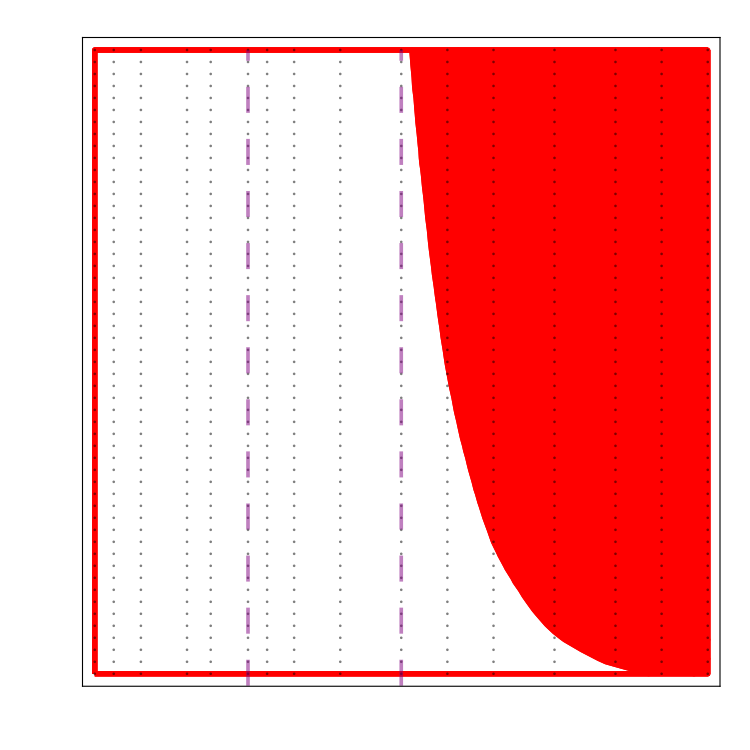

```mathematica
cfFull
```

```mathematica
Log[N[#/1000000]]&/@{10^-3,10^-6}
Line[{{10^-3,0},{10^-3,paramsRanges[[3,-1]]}}]
xLabels
```

{-20.7233,-27.631}

Line[{{1/1000,0},{1/1000,100}}]

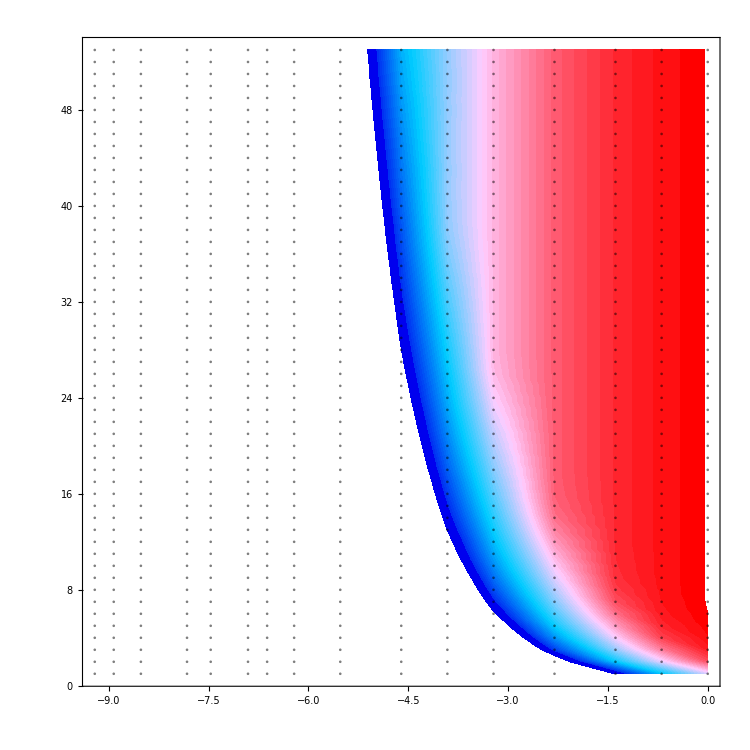

```mathematica
ca=ListContourPlot[tuples
,ClippingStyle->{White,White}
,Contours->50
,ContourStyle->Directive[{Black, Opacity[0]}]
,ColorFunction->(ColorBlend[#]&)
,ColorFunctionScaling->True
,Epilog->Flatten[{PointSize[.0025],Opacity[.5],(Point[#[[1;;2]]]&/@tuples)}]
(*,FrameLabel->(Style[#,50]&/@{"Release Ratio","Weekly Releases"})*)
,FrameStyle->Directive[Black,Opacity[1],Thickness[.005]]
,FrameTicksStyle->30
,FrameTicks->Automatic
,FrameTicks->{{Automatic,None},{xLabels,None}}
,ImageSize->750
,InterpolationOrder->1
,Mesh->None
,MeshStyle->Directive[ White, Opacity[.25]]
(*,PlotLabel->Style["Weeks to: "<>ToString[thresholds[[thresholdIx]]],50,Black]*)
,PlotLegends->None
,PlotRange->{All,All,{Min[weeksRanges//Flatten],Max[weeksRanges//Flatten]}}(*{0, 260}}*)
,PlotRangePadding->None
,TicksStyle->Directive["Label", 14]
]
```

## Export Legend

```mathematica
range=Length[Range[Last[weeksRanges][[2]]-First[weeksRanges[[1]]]]-1];
labels=Range[weeksRanges[[1]],Last[weeksRanges][[2]],2];
blends=ColorBlend[#]&/@Range[0,1,1/range];
colorScale=Transpose[{
Reverse[ImageResize[Rasterize[#]//ImageCrop,50]&/@blends],
Reverse[Style[ToString[#],30]&/@Range[Min[weeksRanges//Flatten],Max[weeksRanges//Flatten]]]
}][[;;;;2]]//Grid;
Export["./img/legend.pdf",colorScale]
(**)
bar=BarLegend[{ColorBlend[#]&,{0,1}}
,LabelStyle->{FontSize->.001}
];
Export["./img/barLegend.pdf",bar]
```

./img/legend.pdf

./img/barLegend.pdf

## Interpolations

```mathematica
i=3;
{thresholdIx,standingVar}={i,100};
filtered=Cases[expTuples,{{_,_,_,standingVar},_}];
tuples={N[#[[1,1]]]/1000000,#[[1,2]],N[#[[2,thresholdIx]]/7]}&/@filtered;
```

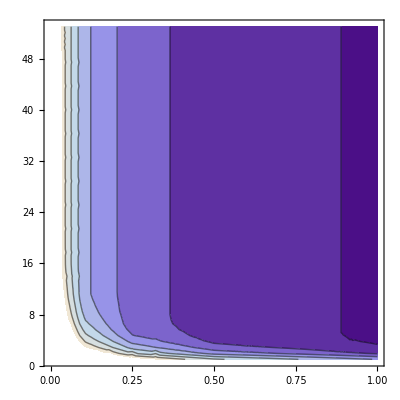

```mathematica
inputTriplets={{#[[1]],#[[2]]},#[[3]]}&/@tuples;
fInter=Interpolation[inputTriplets,Method->"Spline", InterpolationOrder->1];
ContourPlot[
fInter[x,y]
,{x,10^-4,1},{y,1,53}
,ColorFunction->"LakeColors"
]
```

```mathematica
ListPlot3D[tuples
,ColorFunction->"LakeColors"
,ImageSize->1500
,InterpolationOrder->0
,PlotRange->{{0,.1},{0,53},{0,80}}
]
```

-Graphics3D-

0.0631022

{0.0650556,12.5556}

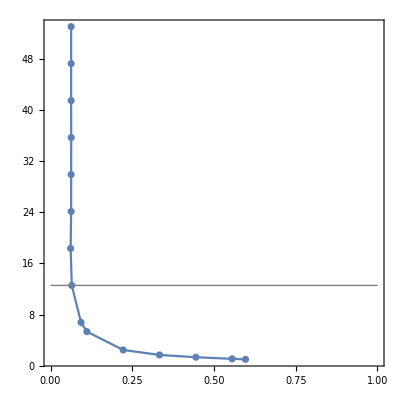

```mathematica
inputTriplets={{#[[1]],#[[2]]},#[[3]]}&/@tuples;
fInter=Interpolation[inputTriplets,Method->"Spline", InterpolationOrder->2];
region=ImplicitRegion[fInter[x,y]==15,{x,y}];
rp=RegionPlot[region,PlotRange->{{10^-4,1},{1,53}}];
pts=rp[[1,1,1]]//Sort;
quant=Quantile[pts[[All,1]],.25]
break=Sort[Cases[pts,{a_,b_}/;a<quant*1.05],#1[[2]]>#2[[2]]&][[-1]]
Show[{rp,pts//ListPlot}
,Epilog->{Gray,Line[{{0,break[[2]]},{1,break[[2]]}}]}
]
```

{{8,5.35962},{9,6.77778},{10,12.5556},{11,12.5556},{12,10.5023},{13,12.5556},{14,12.5556},{15,12.5556},{16,12.5556},{17,18.3333},{18,18.3333},{19,18.3333},{20,18.3333}}

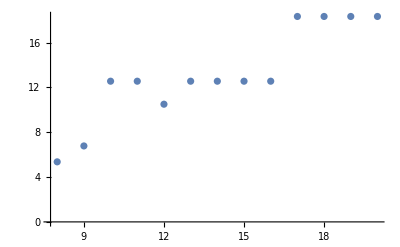

```mathematica
sweep=Table[
region=ImplicitRegion[fInter[x,y]==i,{x,y}];
rp=RegionPlot[region,PlotRange->{{10^-4,1},{1,53}}];
pts=rp[[1,1,1]]//Sort;
quant=Quantile[pts[[All,1]],.25];
break=Sort[Cases[pts,{a_,b_}/;a<quant*1.05],#1[[2]]>#2[[2]]&][[-1]];
{i,break[[2]]}
,{i,8,20}]
ListPlot[sweep]
```